exec(open(<*NotebookDirectory[]*> + "MLRG.py").read())

A rep

up, seg=2.4, 0.01
N=5
mlrg=MLRG(Sn_dat[2],['A1'],[6,12,8]).to(device)
mlrg.load_state_dict(torch.load(<*NotebookDirectory[]*> + "/models/A1/" + "1mlrg_A1.pth", map_location=torch.device('cpu')))
mlrg.eval()
rbm = EquivariantRBM(biadj_dat['cross'], Bond(Sn_dat[2], ['A1']))
J=torch.arange(0.,up,seg).view(-1,1)
JA=J.clone()
Gs=[]
m=[]
for _ in range(N):
	rbm.set_J(J)
	G = GSD(rbm.prob_src(split=True)).view(-1,1)
	Gs.append(torch.cat((JA,G),-1))
	m.append(torch.cat((JA, mlrg.moderator(J).view(-1,1)),1))
	J=mlrg.moderator.RGforward(J)
m=torch.cat(m).view(N,-1,2)
Gs=torch.cat(Gs).view(N,-1,2)

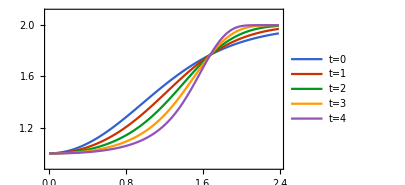
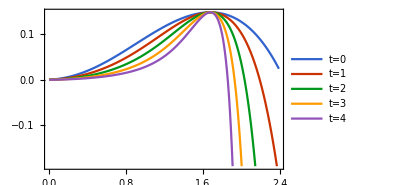

```mathematica
Block[{G,m},
m=ExternalEvaluate[First@ExternalSessions[],"m.tolist()"];
G=ExternalEvaluate[First@ExternalSessions[],"Gs.tolist()"];
Row[{ListPlot[G,Joined->True,PlotRange->{0.9,2.1},PlotMarkers->False,ImageSize->300,PlotLegends->{"t=0","t=1","t=2","t=3","t=4"}],
ListPlot[m,Joined->True,PlotMarkers->False,ImageSize->300,PlotLegends->{"t=0","t=1","t=2","t=3","t=4"}]}]]
```

J=torch.tensor([[1.6]])
#J=mlrg.moderator.RGforward(J)
scals=[]
for _ in range(100):
	J=mlrg.moderator.Newton_step(J,step_size=0.1)
	rbm.set_J(J)
	vals=Tvals(rbm.prob_src(split=True), power=1)
	spec = -vals.abs().log()/(2*torch.pi)
	spec -= spec.min(-1, keepdim=True)[0]
	scals.append(spec[-2].view(-1))
print(J,scals[-1])
scals=torch.cat(scals)

tensor([1.6774]) tensor([0.1204])

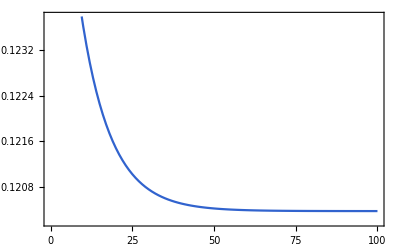

```mathematica
Block[{scals},
scals=ExternalEvaluate[First@ExternalSessions[],"scals.tolist()"];
ListPlot[scals,Joined->True]]
```

A+E rep

up, seg=2.4, 0.01
N=5
mlrg=MLRG(Sn_dat[2],['A1','E'],[12,24,6]).to(device)
mlrg.load_state_dict(torch.load(<*NotebookDirectory[]*> + "/models/A1E/" + "trial0/8mlrg_A1E.pth", map_location=torch.device('cpu')))
mlrg.eval()
JA=torch.arange(0.,up,seg).view(-1,1)
J=torch.zeros(JA.shape[0],5)
J[...,0]+=JA.view(-1)
J0=JA.clone()
dm=[]
m=[]
Gs=[]
rbm = EquivariantRBM(biadj_dat['cross'], Bond(Sn_dat[2], ['A1','E']))
for _ in range(N):
	rbm.set_J(J)
	G=GSD(rbm.prob_src(split=True)).view(-1,1)
	Gs.append(torch.cat((JA,G),-1))
	m.append(torch.cat((J0, mlrg.moderator(J).view(-1,1)),1))
	dm.append(torch.cat((J0, mlrg.moderator.gradC(J).norm(dim=-1).view(-1,1)),1))
	J=mlrg.moderator.RGforward(J)
dm=torch.cat(dm).view(N,-1,2)
m=torch.cat(m).view(N,-1,2)
Gs=torch.cat(Gs).view(N,-1,2)

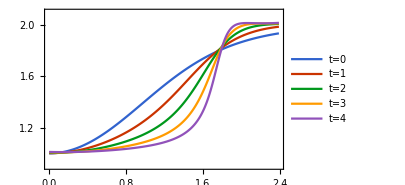
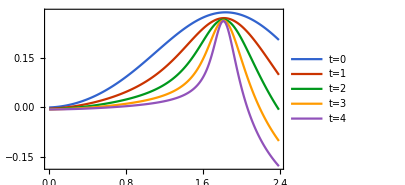
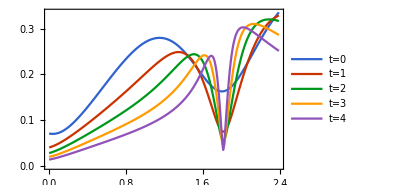

```mathematica
Block[{m,dm,G},
m=ExternalEvaluate[First@ExternalSessions[],"m.tolist()"];
dm=ExternalEvaluate[First@ExternalSessions[],"dm.tolist()"];
G=ExternalEvaluate[First@ExternalSessions[],"Gs.tolist()"];
Row[{ListPlot[G,Joined->True,PlotRange->{0.9,2.1},PlotMarkers->False,ImageSize->300,PlotLegends->{"t=0","t=1","t=2","t=3","t=4"}],
ListPlot[m,Joined->True,PlotMarkers->False,ImageSize->300,PlotLegends->{"t=0","t=1","t=2","t=3","t=4"}],ListPlot[dm,Joined->True,PlotMarkers->False,ImageSize->300,PlotLegends->{"t=0","t=1","t=2","t=3","t=4"}]}]]
```

J=torch.tensor([[1.6,0.,0.,0.,0.]])
#J=mlrg.moderator.RGforward(J)
scals=[]
for _ in range(100):
	J=mlrg.moderator.Newton_step(J,step_size=0.1)
	rbm.set_J(J)
	vals=Tvals(rbm.prob_src(split=True), power=1)
	spec = -vals.abs().log()/(2*torch.pi)
	spec -= spec.min(-1, keepdim=True)[0]
	scals.append(spec[-2].view(-1))
print(J,scals[-1])
scals=torch.cat(scals)

tensor([ 1.7225,  0.2975,  0.2186,  0.3175, -0.0188]) tensor([0.1254])

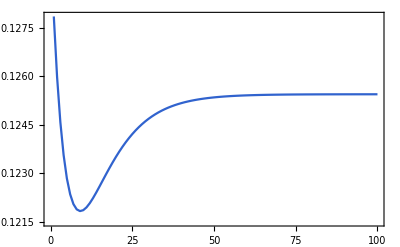

```mathematica
Block[{scals},
scals=ExternalEvaluate[First@ExternalSessions[],"scals.tolist()"];
ListPlot[scals,Joined->True]]
```